```mathematica
CF=4/3;
CA=3;
TR=1/2;
β[x_,ξ_]:=√(1-ξ^-1 4 x/(1-x))
xmax[ξ_]:=1/(1+4/ξ)
C2g1[x_,ξ_]:=Piecewise[{{4 TR/(4π)(Log[(1+β[x,ξ])/(1-β[x,ξ])](-8 x^2 ξ^-2-4x ξ^-1(3x-1)+(2 x^2-2x+1))+β[x,ξ](4 ξ^-1 x(x-1)-(8 x^2-8x+1))), x<xmax[ξ]}, {0, x>=xmax[ξ]}}]
CLg1[x_,ξ_]:=Piecewise[{{16 TR/(4π)(x(1-x)β[x,ξ] - 2 x^2 ξ^-1 Log[(1+β[x,ξ])/(1-β[x,ξ])]), x<xmax[ξ]}, {0, x>=xmax[ξ]}}]
Pgq0[x_]:= 2 CF/(4π) pgq[x]
pgq[x_]:=(2/x−2+x)
Pgg0loc[nf_]:=(CA 11/3-2/3 nf)1/(4π)
Pgg0sing[x_]:= (4CA)/(4π) 1/(1-x)
Pgg0reg[x_]:=(4CA)/(4π)(1/x-2+x-x^2)
β0[nf_]:=1/(4π)(11/3 CA-2/3 nf)
```

```mathematica
C2q21[x_,ξ_]:=NIntegrate[1/z C2g1[z,ξ]Pgq0[x/z],{z,x,xmax[ξ]}]
CLq21[x_,ξ_]:=NIntegrate[1/z CLg1[z,ξ]Pgq0[x/z],{z,x,xmax[ξ]}]
```

```mathematica
C2g21reg[x_,ξ_]:=NIntegrate[1/z C2g1[z,ξ]Pgg0reg[x/z],{z,x,xmax[ξ]}]
C2g21loc[x_,ξ_,nf_]:=N[C2g1[x,ξ]Pgg0loc[nf]]
C2g21sing[x_,ξ_]:=NIntegrate[Pgg0sing[z](1/z C2g1[x/z,ξ]-C2g1[x,ξ]),{z,x,1}] -N[C2g1[x,ξ]]NIntegrate[Pgg0sing[z],{z,0,x}] 
C2g21[x_,ξ_]:=C2g21reg[x,ξ]+C2g21sing[x,ξ](*+C2g21loc[x,ξ,nf]-N[β0[nf] C2g1[x,ξ]]*)
```

```mathematica
CLg21reg[x_,ξ_]:=NIntegrate[1/z CLg1[z,ξ]Pgg0reg[x/z],{z,x,1}]
CLg21loc[x_,ξ_,nf_]:=N[CLg1[x,ξ]Pgg0loc[nf]]
CLg21sing[x_,ξ_]:=NIntegrate[Pgg0sing[z](1/z CLg1[x/z,ξ]-CLg1[x,ξ]),{z,x,1}] - N[CLg1[x,ξ]]NIntegrate[Pgg0sing[z],{z,0,x}]
CLg21[x_,ξ_,nf_]:=(CLg21reg[x,ξ]+CLg21loc[x,ξ,nf]+CLg21sing[x,ξ])-N[β0[nf] CLg1[x,ξ]]
CLg21[x_,ξ_]:=CLg21reg[x,ξ]+CLg21sing[x,ξ](*+CLg21loc[x,ξ,nf]-N[β0[nf] CLg1[x,ξ]]*)
```

```mathematica
data2 = Import["/Users/niccololaurenti/Master-thesis/extras/mu_dep_parts/xi=2.dat"];
data20 = Import["/Users/niccololaurenti/Master-thesis/extras/mu_dep_parts/xi=20.dat"];
```

```mathematica
C2g21apfel2=data2[[All,{1,2}]];
C2q21apfel2=data2[[All,{1,3}]];

C2g21apfel20=data20[[All,{1,2}]];
C2q21apfel20=data20[[All,{1,3}]];

CLg21apfel2=data2[[All,{1,4}]];
CLq21apfel2=data2[[All,{1,5}]];

CLg21apfel20=data20[[All,{1,4}]];
CLq21apfel20=data20[[All,{1,5}]];
```

```mathematica
C2g21list2=Table[{x,-C2g21[x,2,3]},{x,0.001,xmax[2],0.001}];
C2g21list20=Table[{x,-C2g21[x,20,3]},{x,0.001,xmax[20],0.001}];
```

```mathematica
CLg21list2=Table[{x,-CLg21[x,2,3]},{x,0.001,xmax[2],0.001}];
CLg21list20=Table[{x,-CLg21[x,20,3]},{x,0.001,xmax[20],0.001}];
```

```mathematica
C2q21list2=Table[{x,-C2q21[x,2]},{x,0.001,xmax[2],0.001}];
C2q21list20=Table[{x,-C2q21[x,20]},{x,0.001,xmax[20],0.001}];
```

```mathematica
CLq21list2=Table[{x,-CLq21[x,2]},{x,0.001,xmax[2],0.001}];
CLq21list20=Table[{x,-CLq21[x,20]},{x,0.001,xmax[20],0.001}];
```

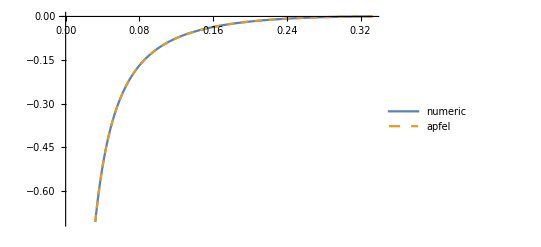

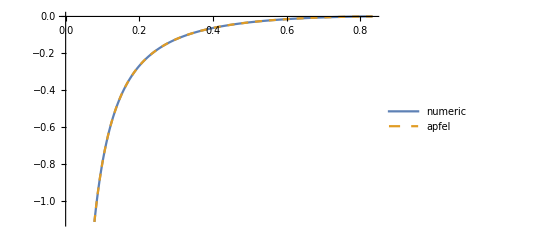

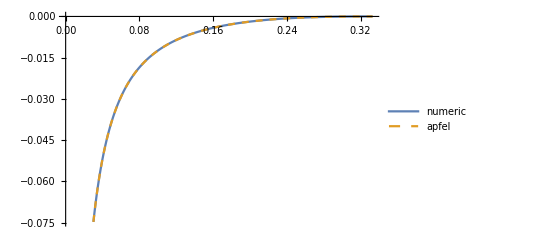

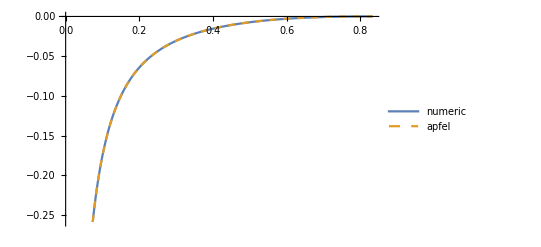

```mathematica
ListLinePlot[{C2q21list2,C2q21apfel2},PlotLegends->{"numeric","apfel"},PlotStyle->{,Dashed }]
ListLinePlot[{C2q21list20,C2q21apfel20},PlotLegends->{"numeric","apfel"},PlotStyle->{,Dashed  }]
ListLinePlot[{CLq21list2,CLq21apfel2},PlotLegends->{"numeric","apfel"},PlotStyle->{,Dashed }]
ListLinePlot[{CLq21list20,CLq21apfel20},PlotLegends->{"numeric","apfel"},PlotStyle->{,Dashed }]
```

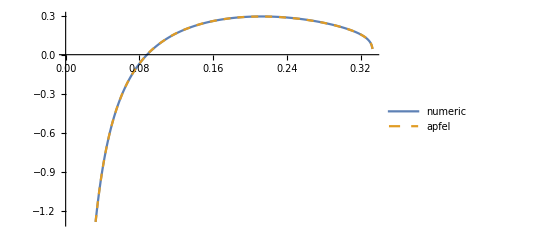

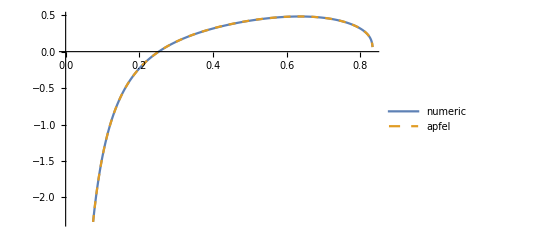

```mathematica
ListLinePlot[{C2g21list2,C2g21apfel2},PlotLegends->{"numeric","apfel"},PlotStyle->{,Dashed  }]
ListLinePlot[{C2g21list20, C2g21apfel20},PlotLegends->{"numeric","apfel"}, PlotStyle->{,Dashed  }]
```

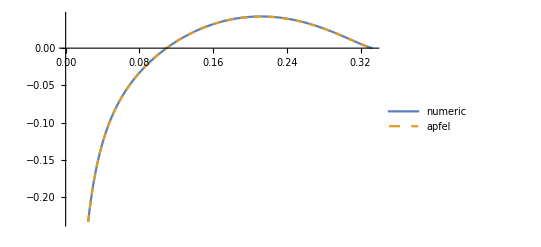

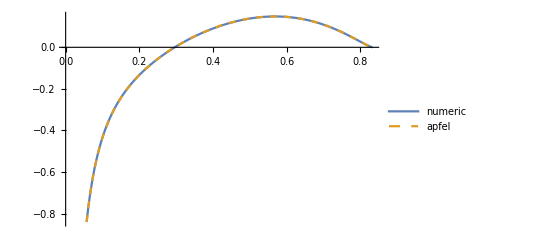

```mathematica
ListLinePlot[{CLg21list2,CLg21apfel2},PlotLegends->{"numeric","apfel"},PlotStyle->{,Dashed  }]
ListLinePlot[{CLg21list20, CLg21apfel20},PlotLegends->{"numeric","apfel"}, PlotStyle->{,Dashed  }]
```